```mathematica
Quit[]
```

# Diagram manipulation

## Settings

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m";
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m";
Remove[q1];
Remove[q2];
<<"/home/riccardo/Programs/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

ABISS: A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/EWProcesses/ll_triangles_photon/input/kinematics.m.

```mathematica
userIntegralMasses[userIntegralFamiliesNames]
```

userIntegralMasses[{A0,B0,C0,D0}]

## Diagram generation

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish_var", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

```mathematica
process={F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]};
```

```mathematica
topologiesBorn=CreateTopologies[0,2->2,ExcludeTopologies->Tadpoles];
fieldsBorn=InsertFields[topologiesBorn, process];
fieldsBorn=DiagramSelect[fieldsBorn,!FreeQ[#,Field[5]->V[10]]&];
topologies1L=CreateTopologies[1,2-> 2,ExcludeTopologies->{Tadpoles,Boxes,WFCorrections}];
topologies1L=topologies1L[[0]][topologies1L[[1]]];
fields1L=InsertFields[topologies1L, process];
fields1L=DiagramSelect[fields1L,!FreeQ[#,Field[5]->V[10]]&];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish_var.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish_var} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 24 field point(s)

in total: 4 Particles insertions

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 43 Particles insertions

Restoring 24 field point(s)

in total: 43 Particles insertions

## Paint

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

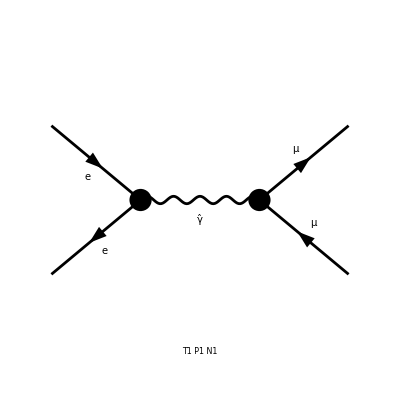

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

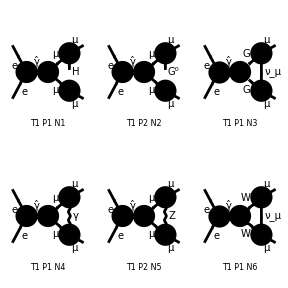

```mathematica
Paint[fieldsBorn];
Paint[fields1L];
```

## Manipulations

### Master Integral and Coefficients

```mathematica
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m");
Length[masters]
```

18

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,6}]
```

### Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m")  ;
electronParameters={I3l1->-1/2,Ql1->-1};
```

### Born Squared matrix element

```mathematica
myAmpBorn=<<(NotebookDirectory[]<>"feynArts_amplitudes/BornAmplitudes.m")
```

{v̄[p2,0].(ⅈ EL gAl[1] (ga[Lor1].om_-+ga[Lor1].om_+)).u[p1,0] ū[k1,MM].(ⅈ EL gAl[2] (ga[Lor2].om_-+ga[Lor2].om_+)).v[k2,MM] g[Lor1,Lor2] 1/(k1+k2)^2}

```mathematica
smBorn=AmpSquare[myAmpBorn,myAmpBorn]
```

{(EL^4 (4 mm^4+2 (-2+d) mm^2 s-2 s^2+d s^2+4 s t+4 t^2-2 mm^2 ((-2+d) s+4 t)) gAl[1]^2 gAl[2]^2)/s^2}

```mathematica
smBornR=smBorn/.parameterReplace/.electronParameters//Expand//FullSimplify
```

{(EL^4 Ql2^2 ((-2+d) s^2+4 (mm^4-2 mm^2 t+t (s+t))))/s^2}

```mathematica
prefactor=EL^4/s^2
```

EL^4/s^2

### Parameter replace

```mathematica
diagramCoefficientsR=diagramCoefficients/.parameterReplace/.electronParameters;
```

Save result

```mathematica
diagramCoefficientsR>>(NotebookDirectory[]<>"coefficients/coefficientsR.m");
```

Load result

```mathematica
diagramCoefficientsR=<<(NotebookDirectory[]<>"coefficients/coefficientsR.m");
```

### Remove Prefactor

```mathematica
smBornA=smBornR/prefactor
```

{Ql2^2 ((-2+d) s^2+4 (mm^4-2 mm^2 t+t (s+t)))}

```mathematica
diagramCoefficientsA=diagramCoefficientsR/prefactor
```

{{(s^2 (39+1+(ⅈ EL^6 mm^2 Ql2^2 (1))/(32 (-2+d) mw^2 π^4 s 1^2 sw^2)))/EL^4,(s^2 (32+1/(32 5 sw^2)))/EL^4,(s^2 (30+1))/EL^4,(s^2 (1))/EL^4,(s^2 (1))/EL^4,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,8,0,0,0,0,0},2,{0,16,0},{0,0,0,0,0,9,0,0,0,0}}
 |  |  |  |

#### Calculate reduced coefficients and save

```mathematica
diagramCoefficientsA=diagramCoefficientsA//Expand//Simplify;
```

Save result

```mathematica
diagramCoefficientsA>>(NotebookDirectory[]<>"coefficients/coefficientsA.m");
```

#### Load reduced coefficients

Load result

```mathematica
diagramCoefficientsA=<<(NotebookDirectory[]<>"coefficients/coefficientsA.m");
```

### Equal masters

```mathematica
Do[
If[sameIntegral[masters[[i]],masters[[j]]]&&i<j,
Print[ToString[i]<>" "<>ToString[j]]
],
{i,Length[masters]},{j,Length[masters]}]
```

3 8

3 17

4 9

8 17

### Delete Duplicates

```mathematica
diagramCoefficientsND=Map[deleteUIDuplicates[#,masters][[1]]&,diagramCoefficientsA];
```

```mathematica
mastersND=deleteUIDuplicates[diagramCoefficientsA[[1]],masters][[2]]
```

{userIntegral[A0,{mh,mm},1,1,1,0],userIntegral[A0,{mh,mm},1,1,0,0],userIntegral[A0,{mh,mm},0,1,1,0],userIntegral[A0,{mh,mm},0,1,0,0],userIntegral[A0,{mh,mm},1,0,0,0],userIntegral[A0,{mz,mm},1,1,1,0],userIntegral[A0,{mz,mm},1,1,0,0],userIntegral[A0,{mz,mm},1,0,0,0],userIntegral[B0,{mw},1,1,0,0],userIntegral[B0,{mw},0,1,1,0],userIntegral[B0,{mw},1,1,1,0],userIntegral[A0,{mw,m2},1,0,0,0],userIntegral[B0,{mm},1,1,1,0],userIntegral[B0,{mm},1,1,0,0],userIntegral[A0,{mm,m2},1,0,0,0]}

## Terms

```mathematica
coeffQ0=Coefficient[diagramCoefficientsND,Ql2,0];
coeffQ1=Coefficient[diagramCoefficientsND,Ql2,1];
coeffQ2=Coefficient[diagramCoefficientsND,Ql2,2];
coeffQ3=Coefficient[diagramCoefficientsND,Ql2,3];
coeffQ4=Coefficient[diagramCoefficientsND,Ql2,4];
```

```mathematica
nullCoeffList={};
Do[nullCoeffList=Append[nullCoeffList,0],Length[mastersND]];
nullCoeffList
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Do[If[coeffQ0[[i]]=!=nullCoeffList,Print[i]],{i,Length[coeffQ1]}]
```

```mathematica
Do[If[coeffQ1[[i]]=!=nullCoeffList,Print[i]],{i,Length[coeffQ1]}]
```

3

6

```mathematica
Do[If[coeffQ2[[i]]=!=nullCoeffList,Print[i]],{i,Length[coeffQ2]}]
```

1

2

5

```mathematica
Do[If[coeffQ3[[i]]=!=nullCoeffList,Print[i]],{i,Length[coeffQ3]}]
```

5

```mathematica
Do[If[coeffQ4[[i]]=!=nullCoeffList,Print[i]],{i,Length[coeffQ4]}]
```

4

5

## Q^4 terms

## Not null terms

```mathematica
notZero[0]:=0
notZero[expr_]:=1
```

```mathematica
Map[notZero,coeffQ0,{2}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Map[notZero,coeffQ1,{2}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0)

```mathematica
Map[notZero,coeffQ2,{2}]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Map[notZero,coeffQ3,{2}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Map[notZero,coeffQ4,{2}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
scalarIntegral[mastersND[[3]]]
```

1/((-mm^2+(p3+q1)^2) (-mm^2+(-p1-p2+p3+q1)^2))

```mathematica
scalarIntegral[mastersND[[4]]]
```

1/(-mm^2+(p3+q1)^2)

## Diagram Analysis

### W Boson and Goldstone G

W Boson

```mathematica
c1=coeffQ1[[3,10]] /.s->2*mm^2-t-u/.d->4//FullSimplify
```

(ⅈ EL^2 mm^2 (48 mm^8-8 mm^6 (4 mw^2-3 t+u)+(t+u) (2 mw^2+t+u) (t^2+u^2)-2 mm^4 (t^2+mw^2 (6 t-2 u)+22 t u+5 u^2)-4 mm^2 (2 t^3+t^2 u+u^3+mw^2 (3 t^2-12 t u+u^2))))/(64 mw^2 π^4 sw^2 (2 mm^2+t+u)^2)

```mathematica
c2=coeffQ1[[6,10]]/.s->2*mm^2-t-u/.d->4//FullSimplify
```

1/(32 π^4 sw^2 (2 mm^2+t+u)^2)ⅈ EL^2 (16 mm^8-8 mm^6 (4 mw^2-5 t+3 u)+2 mm^4 (11 t^2-14 t u+7 u^2+2 mw^2 (-3 t+u))+(t+u) (t^2+u^2) (2 mw^2-3 (t+u))-4 mm^2 (t (3 t-u) (t+u)+mw^2 (3 t^2-12 t u+u^2)))

```mathematica
denominator=64 2  π^4 sw^2 (2 mm^2+t+u)^2;(* 4*mm^2-s *)
```

```mathematica
Collect[denominator c1//Expand//Simplify,{I,EL,mw,mm,t,u,d}]
```

1/mw^2 2 ⅈ EL^2 mm^2 (48 mm^8-8 mm^6 (4 mw^2-3 t+u)-2 mm^4 (t^2+mw^2 (6 t-2 u)+22 t u+5 u^2)+(2 mw^2+t+u) (t^3+t^2 u+t u^2+u^3)-4 mm^2 (2 t^3+t^2 u+u^3+mw^2 (3 t^2-12 t u+u^2)))

```mathematica
Collect[denominator c2//Expand//Simplify,{I,EL,mw,mm,t,u,d}]
```

4 ⅈ EL^2 (16 mm^8-8 mm^6 (4 mw^2-5 t+3 u)+mm^4 (22 t^2-28 t u+14 u^2+4 mw^2 (-3 t+u))+(t^3+t^2 u+t u^2+u^3) (2 mw^2-3 (t+u))-4 mm^2 (t (3 t^2+2 t u-u^2)+mw^2 (3 t^2-12 t u+u^2)))

```mathematica
Collect[((c1+c2)denominator)//Expand//Simplify,{I,EL,mw,mm,t,u,d}]
```

1/mw^2 2 ⅈ EL^2 (48 mm^10+8 mm^8 (3 t-u)+2 mw^2 (t^3+t^2 u+t u^2+u^3) (2 mw^2-3 (t+u))-2 mm^6 (32 mw^4+t^2+22 t u+5 u^2+mw^2 (-34 t+22 u))-4 mm^4 (2 t^3+mw^4 (6 t-2 u)+t^2 u+u^3+mw^2 (-8 t^2+2 t u-6 u^2))+mm^2 ((t+u)^2 (t^2+u^2)-8 mw^4 (3 t^2-12 t u+u^2)-2 mw^2 (11 t^3+7 t^2 u-5 t u^2-u^3)))

```mathematica
Coefficient[denominator c1,t,4]//Simplify
```

(2 ⅈ EL^2 mm^2)/mw^2

```mathematica
Coefficient[denominator c2,t,4]//Simplify
```

-12 ⅈ EL^2

```mathematica
Coefficient[denominator c1,t,3]//Simplify
```

(4 ⅈ EL^2 mm^2 (-4 mm^2+mw^2+u))/mw^2

```mathematica
Coefficient[denominator c2,t,3]//Simplify
```

-8 ⅈ EL^2 (6 mm^2-mw^2+3 u)

```mathematica
Coefficient[denominator c1,t,2]//Simplify
```

-(4 ⅈ EL^2 mm^2 (mm^4-u (mw^2+u)+2 mm^2 (3 mw^2+u)))/mw^2

```mathematica
Coefficient[denominator c2,t,2]//Simplify
```

8 ⅈ EL^2 (11 mm^4+(mw^2-3 u) u-2 mm^2 (3 mw^2+2 u))

```mathematica
Coefficient[denominator c1,t,1]//Simplify
```

(4 ⅈ EL^2 mm^2 (12 mm^6+24 mm^2 mw^2 u+u^2 (mw^2+u)-2 mm^4 (3 mw^2+11 u)))/mw^2

```mathematica
Coefficient[denominator c2,t,1]//Simplify
```

8 ⅈ EL^2 (20 mm^6+(mw^2-3 u) u^2+2 mm^2 u (12 mw^2+u)-2 mm^4 (3 mw^2+7 u))

```mathematica
Coefficient[denominator c1,t,0]//Simplify
```

(2 ⅈ EL^2 mm^2 (48 mm^8+2 mm^4 (2 mw^2-5 u) u-4 mm^2 u^2 (mw^2+u)+u^3 (2 mw^2+u)-8 mm^6 (4 mw^2+u)))/mw^2

```mathematica
Coefficient[denominator c2,t,0]//Simplify
```

4 ⅈ EL^2 (16 mm^8-4 mm^2 mw^2 u^2+(2 mw^2-3 u) u^3-8 mm^6 (4 mw^2+3 u)+2 mm^4 u (2 mw^2+7 u))

Fattori di proporzionalità

```mathematica
a1=6 mw^2/mm^2
a2=2 mw^2/mm^2
```

(6 mw^2)/mm^2

(2 mw^2)/mm^2

### Higgs Boson

```mathematica
scalarIntegral[mastersND[[1]]]
scalarIntegral[mastersND[[2]]]
scalarIntegral[mastersND[[3]]]
scalarIntegral[mastersND[[4]]]
scalarIntegral[mastersND[[5]]]
```

1/((-mh^2+q1^2) (-mm^2+(p3+q1)^2) (-mm^2+(-p1-p2+p3+q1)^2))

1/((-mh^2+q1^2) (-mm^2+(p3+q1)^2))

1/((-mm^2+(p3+q1)^2) (-mm^2+(-p1-p2+p3+q1)^2))

1/(-mm^2+(p3+q1)^2)

1/(-mh^2+q1^2)

```mathematica
coeffQ2[[1,1]]/.s->2*mm^2-t-u/.d->4//FullSimplify
coeffQ2[[1,2]]/.s->2*mm^2-t-u/.d->4//FullSimplify
coeffQ2[[1,5]]/.s->2*mm^2-t-u/.d->4//FullSimplify
```

(ⅈ EL^2 mm^2 (-2 mh^2 mm^2 (10 mm^4+t (3 t-13 u)+2 mm^2 (t-u)) (2 mm^2+t+u)+mm^2 (2 mm^2+t+u)^2 (20 mm^4-mm^2 (11 t+17 u)+4 (t^2+u^2))+mh^4 (16 mm^6+mm^4 (6 t-2 u)-(t+u) (t^2+u^2)+2 mm^2 (3 t^2-12 t u+u^2))))/(32 mw^2 π^4 sw^2 (2 mm^2+t+u)^2)

(ⅈ EL^2 mm^2 (4 mm^2 (2 mm^2+t+u) (6 mm^4+t (t-9 u)-mm^2 (t+u))+mh^2 (-56 mm^6-4 mm^4 (7 t+u)+8 mm^2 t (-2 t+9 u)+(t+u) (t^2+12 t u+3 u^2))))/(64 mw^2 π^4 sw^2 (2 mm^2+t+u)^2)

(ⅈ EL^2 mm^2 (12 mm^4+t^2+2 mm^2 (t-u)-12 t u-u^2))/(64 mw^2 π^4 sw^2 (2 mm^2+t+u))

### Z and G^0

Integrals caontaining Z boson mass

```mathematica
scalarIntegral[mastersND[[6]]]
scalarIntegral[mastersND[[7]]]
scalarIntegral[mastersND[[8]]]
```

1/((-mz^2+q1^2) (-mm^2+(p3+q1)^2) (-mm^2+(-p1-p2+p3+q1)^2))

1/((-mz^2+q1^2) (-mm^2+(p3+q1)^2))

1/(-mz^2+q1^2)

```mathematica
c3=coeffQ2[[2,6]] /.s->2*mm^2-t-u//FullSimplify
```

-((ⅈ EL^2 mm^2 (-32 (-2+d) mm^10+mz^2 (t+u) ((-2+d) t^2+2 (-4+d) t u+(-2+d) u^2) (2 mz^2+(-4+d) (t+u))+8 mm^8 (2 (14+(-7+d) d) mz^2-(-2+d) (t+3 u))-4 mm^2 (-mz^2 t (t+u) (3 (-2+d) t+(2-3 d) u)+mz^4 (3 (-2+d) t^2-8 (-1+d) t u+(-2+d) u^2))-2 mm^4 (4 mz^4 ((-5+2 d) t-u)-(-2+d) (t+u)^2 (3 t+u)+2 mz^2 ((28+d (-17+2 d)) t^2+4 (13+(-6+d) d) t u+(24+d (-15+2 d)) u^2))-16 mm^6 (mz^2 (-3 t+u)+2 t (t+u)+d (mz^4+mz^2 (t-u)-t (t+u)))))/(64 (-2+d) mw^2 π^4 sw^2 (2 mm^2+t+u)^2))

```mathematica
c4=coeffQ2[[5,6]]/.s->2*mm^2-t-u//FullSimplify
```

(ⅈ EL^2 I3l2^2 (32 (-2+d) (-1+d) mm^10-8 mm^8 (2 (22+(-9+d) d) mz^2-(6+d) t+(-2+d) u)-(t+u) ((-2+d) t^2+2 (-4+d) t u+(-2+d) u^2) (2 mz^4+(-8+d) mz^2 (t+u)+2 (t+u)^2)+2 mm^4 (4 mz^4 ((-5+2 d) t-u)+(t+u) ((-26+9 d) t^2-24 t u+7 (-2+d) u^2)+2 mz^2 ((52+d (-27+2 d)) t^2+4 (23+(-8+d) d) t u+(-8+d) (-5+2 d) u^2))-16 mm^6 (mz^2 (t-3 u)+4 (t+u)^2+d^2 (t+u)^2-d (mz^4+5 t^2+7 t u+4 u^2-mz^2 (t+u)))+2 mm^2 (-2 mz^2 (t+u) ((-8+3 d) t^2+(10-7 d) t u+2 u^2)+2 mz^4 (3 (-2+d) t^2-8 (-1+d) t u+(-2+d) u^2)+(t+u)^2 (d^2 (t+u)^2+4 u (5 t+u)-4 d (t^2+3 t u+u^2)))))/(32 CW^2 π^4 SW^2 (2 mm^2+t+u)^2)

```mathematica
denominator=64 (-2+d)  π^4 sw^2 (2 mm^2+t+u)^2;(* 4*mm^2-s *)
```

```mathematica
Collect[denominator c3//Expand//Simplify,{I,EL,mw,mm,t,u,d}]
```

-1/((-2+d) mw^2)2 ⅈ EL^2 mm^2 (-32 (-2+d) mm^10+mz^2 (t+u) ((-2+d) t^2+2 (-4+d) t u+(-2+d) u^2) (2 mz^2+(-4+d) (t+u))+8 mm^8 (2 (14-7 d+d^2) mz^2-(-2+d) (t+3 u))-4 mm^2 (-mz^2 t (t+u) (3 (-2+d) t+(2-3 d) u)+mz^4 (3 (-2+d) t^2-8 (-1+d) t u+(-2+d) u^2))-2 mm^4 (4 mz^4 ((-5+2 d) t-u)-(-2+d) (t+u)^2 (3 t+u)+2 mz^2 ((28-17 d+2 d^2) t^2+4 (13-6 d+d^2) t u+(24-15 d+2 d^2) u^2))-16 mm^6 (mz^2 (-3 t+u)+2 t (t+u)+d (mz^4+mz^2 (t-u)-t (t+u))))

```mathematica
Collect[denominator c4//Expand//Simplify,{I,EL,mw,mm,t,u,d}]
```

1/(CW^2 SW^2)4 ⅈ EL^2 I3l2^2 sw^2 (32 (2-3 d+d^2) mm^10-8 mm^8 (2 (22-9 d+d^2) mz^2-(6+d) t+(-2+d) u)-(t+u) ((-2+d) t^2+2 (-4+d) t u+(-2+d) u^2) (2 mz^4+(-8+d) mz^2 (t+u)+2 (t+u)^2)+2 mm^4 (4 mz^4 ((-5+2 d) t-u)+(t+u) ((-26+9 d) t^2-24 t u+7 (-2+d) u^2)+2 mz^2 ((52-27 d+2 d^2) t^2+4 (23-8 d+d^2) t u+(40-21 d+2 d^2) u^2))-16 mm^6 (mz^2 (t-3 u)+4 (t+u)^2+d^2 (t+u)^2-d (mz^4+5 t^2+7 t u+4 u^2-mz^2 (t+u)))+2 mm^2 (-2 mz^2 (t+u) ((-8+3 d) t^2+(10-7 d) t u+2 u^2)+2 mz^4 (3 (-2+d) t^2-8 (-1+d) t u+(-2+d) u^2)+(t+u)^2 (d^2 (t+u)^2+4 u (5 t+u)-4 d (t^2+3 t u+u^2))))

```mathematica
Collect[((c3+c4)denominator)//Expand//Simplify,{I,EL,mw,mm,t,u,d}]
```

-1/(CW^2 (-2+d) mw^2 SW^2)2 ⅈ EL^2 (CW^2 mm^2 SW^2 (-32 (-2+d) mm^10+mz^2 (t+u) ((-2+d) t^2+2 (-4+d) t u+(-2+d) u^2) (2 mz^2+(-4+d) (t+u))+8 mm^8 (2 (14-7 d+d^2) mz^2-(-2+d) (t+3 u))-4 mm^2 mz^2 (-t (t+u) (3 (-2+d) t+(2-3 d) u)+mz^2 (3 (-2+d) t^2-8 (-1+d) t u+(-2+d) u^2))-2 mm^4 (4 mz^4 ((-5+2 d) t-u)-(-2+d) (t+u)^2 (3 t+u)+2 mz^2 ((28-17 d+2 d^2) t^2+4 (13-6 d+d^2) t u+(24-15 d+2 d^2) u^2))-16 mm^6 (mz^2 (-3 t+u)+2 t (t+u)+d (mz^4+mz^2 (t-u)-t (t+u))))-2 I3l2^2 mw^2 sw^2 (32 (-2+d)^2 (-1+d) mm^10-8 (-2+d) mm^8 (2 (22-9 d+d^2) mz^2-(6+d) t+(-2+d) u)-(t+u) ((-2+d) t^2+2 (-4+d) t u+(-2+d) u^2) (2 (-2+d) mz^4+(16-10 d+d^2) mz^2 (t+u)+2 (-2+d) (t+u)^2)+2 (-2+d) mm^4 (4 mz^4 ((-5+2 d) t-u)+(t+u) ((-26+9 d) t^2-24 t u+7 (-2+d) u^2)+2 mz^2 ((52-27 d+2 d^2) t^2+4 (23-8 d+d^2) t u+(40-21 d+2 d^2) u^2))-16 (-2+d) mm^6 (mz^2 (t-3 u)+4 (t+u)^2+d^2 (t+u)^2-d (mz^4+5 t^2+7 t u+4 u^2-mz^2 (t+u)))+2 (-2+d) mm^2 (-2 mz^2 (t+u) ((-8+3 d) t^2+(10-7 d) t u+2 u^2)+2 mz^4 (3 (-2+d) t^2-8 (-1+d) t u+(-2+d) u^2)+(t+u)^2 (d^2 (t+u)^2+4 u (5 t+u)-4 d (t^2+3 t u+u^2)))))

```mathematica
Coefficient[denominator c3,t,4]
```

-(2 ⅈ EL^2 mm^2 (8 mz^2-6 d mz^2+d^2 mz^2))/((-2+d) mw^2)

```mathematica
Coefficient[denominator c4,t,4]
```

(4 ⅈ EL^2 I3l2^2 sw^2 (-8 d mm^2+2 d^2 mm^2-16 mz^2+10 d mz^2-d^2 mz^2+28 u-10 d u))/(CW^2 SW^2)

```mathematica
Coefficient[denominator c3,t,3]
```

-(2 ⅈ EL^2 mm^2 (-12 mm^4+6 d mm^4-24 mm^2 mz^2+12 d mm^2 mz^2-4 mz^4+2 d mz^4+48 mz^2 u-28 d mz^2 u+4 d^2 mz^2 u))/((-2+d) mw^2)

```mathematica
Coefficient[denominator c4,t,3]
```

1/(CW^2 SW^2)4 ⅈ EL^2 I3l2^2 sw^2 (-52 mm^4+18 d mm^4+32 mm^2 mz^2-12 d mm^2 mz^2+4 mz^4-2 d mz^4+40 mm^2 u-40 d mm^2 u+8 d^2 mm^2 u-96 mz^2 u+44 d mz^2 u-4 d^2 mz^2 u+64 u^2-20 d u^2)

```mathematica
Coefficient[denominator c3,t,2]
```

-1/((-2+d) mw^2)2 ⅈ EL^2 mm^2 (-32 mm^6+16 d mm^6-112 mm^4 mz^2+68 d mm^4 mz^2-8 d^2 mm^4 mz^2+24 mm^2 mz^4-12 d mm^2 mz^4-28 mm^4 u+14 d mm^4 u-16 mm^2 mz^2 u-20 mz^4 u+6 d mz^4 u+80 mz^2 u^2-44 d mz^2 u^2+6 d^2 mz^2 u^2)

```mathematica
Coefficient[denominator c4,t,2]
```

1/(CW^2 SW^2)4 ⅈ EL^2 I3l2^2 sw^2 (-64 mm^6+80 d mm^6-16 d^2 mm^6+208 mm^4 mz^2-108 d mm^4 mz^2+8 d^2 mm^4 mz^2-24 mm^2 mz^4+12 d mm^2 mz^4-100 mm^4 u+18 d mm^4 u-8 mm^2 mz^2 u+16 d mm^2 mz^2 u+20 mz^4 u-6 d mz^4 u+88 mm^2 u^2-64 d mm^2 u^2+12 d^2 mm^2 u^2-160 mz^2 u^2+68 d mz^2 u^2-6 d^2 mz^2 u^2+64 u^3-20 d u^3)

```mathematica
Coefficient[denominator c3,t,1]
```

-1/((-2+d) mw^2)2 ⅈ EL^2 mm^2 (16 mm^8-8 d mm^8+48 mm^6 mz^2-16 d mm^6 mz^2+40 mm^4 mz^4-16 d mm^4 mz^4-32 mm^6 u+16 d mm^6 u-208 mm^4 mz^2 u+96 d mm^4 mz^2 u-16 d^2 mm^4 mz^2 u-32 mm^2 mz^4 u+32 d mm^2 mz^4 u-20 mm^4 u^2+10 d mm^4 u^2+8 mm^2 mz^2 u^2-12 d mm^2 mz^2 u^2-20 mz^4 u^2+6 d mz^4 u^2+48 mz^2 u^3-28 d mz^2 u^3+4 d^2 mz^2 u^3)

```mathematica
Coefficient[denominator c4,t,1]
```

1/(CW^2 SW^2)4 ⅈ EL^2 I3l2^2 sw^2 (48 mm^8+8 d mm^8-16 mm^6 mz^2-16 d mm^6 mz^2-40 mm^4 mz^4+16 d mm^4 mz^4-128 mm^6 u+112 d mm^6 u-32 d^2 mm^6 u+368 mm^4 mz^2 u-128 d mm^4 mz^2 u+16 d^2 mm^4 mz^2 u+32 mm^2 mz^4 u-32 d mm^2 mz^4 u-76 mm^4 u^2+14 d mm^4 u^2-48 mm^2 mz^2 u^2+28 d mm^2 mz^2 u^2+20 mz^4 u^2-6 d mz^4 u^2+56 mm^2 u^3-40 d mm^2 u^3+8 d^2 mm^2 u^3-96 mz^2 u^3+44 d mz^2 u^3-4 d^2 mz^2 u^3+28 u^4-10 d u^4)

```mathematica
Coefficient[denominator c3,t,0]
```

-1/((-2+d) mw^2)2 ⅈ EL^2 mm^2 (64 mm^10-32 d mm^10+224 mm^8 mz^2-112 d mm^8 mz^2+16 d^2 mm^8 mz^2-16 d mm^6 mz^4+48 mm^8 u-24 d mm^8 u-16 mm^6 mz^2 u+16 d mm^6 mz^2 u+8 mm^4 mz^4 u-96 mm^4 mz^2 u^2+60 d mm^4 mz^2 u^2-8 d^2 mm^4 mz^2 u^2+8 mm^2 mz^4 u^2-4 d mm^2 mz^4 u^2-4 mm^4 u^3+2 d mm^4 u^3-4 mz^4 u^3+2 d mz^4 u^3+8 mz^2 u^4-6 d mz^2 u^4+d^2 mz^2 u^4)

```mathematica
Coefficient[denominator c4,t,0]
```

1/(CW^2 SW^2)4 ⅈ EL^2 I3l2^2 sw^2 (64 mm^10-96 d mm^10+32 d^2 mm^10-352 mm^8 mz^2+144 d mm^8 mz^2-16 d^2 mm^8 mz^2+16 d mm^6 mz^4+16 mm^8 u-8 d mm^8 u+48 mm^6 mz^2 u-16 d mm^6 mz^2 u-8 mm^4 mz^4 u-64 mm^6 u^2+64 d mm^6 u^2-16 d^2 mm^6 u^2+160 mm^4 mz^2 u^2-84 d mm^4 mz^2 u^2+8 d^2 mm^4 mz^2 u^2-8 mm^2 mz^4 u^2+4 d mm^2 mz^4 u^2-28 mm^4 u^3+14 d mm^4 u^3-8 mm^2 mz^2 u^3+4 mz^4 u^3-2 d mz^4 u^3+8 mm^2 u^4-8 d mm^2 u^4+2 d^2 mm^2 u^4-16 mz^2 u^4+10 d mz^2 u^4-d^2 mz^2 u^4+4 u^5-2 d u^5)

## Analogous Integral Families

```mathematica
sameIntegral[ui1_userIntegral,ui2_userIntegral]:=Module[{test1,test2},
test1=scalarIntegral[ui1];
test2=scalarIntegral[ui2];
Return[test1===test2];
]
```

## Functions

```mathematica
massIndex[mi_]:=ToExpression[StringDrop[ToString[mi],1]]
```

```mathematica
massSub[0,ui_userIntegral]:=0;
massSub[mi_,ui_userIntegral]:=ui[[2,massIndex[mi]]];
```

```mathematica
masses[ui_userIntegral]:=Module[{masses,massesReplace},
masses=Map[massSub[#,ui]&,userIntegralMasses[ui[[1]]]];
Return[masses]
]
```

```mathematica
extractIndices[ui_userIntegral]:=Delete[List@@ui,{{1},{2}}]
```

```mathematica
scalarIntegral[ui_userIntegral]:=Module[{if,si},
if=ui[[1]];
si=userPropagatorMomenta[if]^2-masses[ui]^2;
si=si^extractIndices[ui];
Return[1/(Times@@si)];
]
```

## Master delete duplicates

```mathematica
deleteUIDuplicates[coefficients_List,masters_List]:=Module[{newMasters,newCoefficients,sameAs},
newMasters={masters[[1]]};
newCoefficients={coefficients[[1]]};
Do[
sameAs=0;
Do[
If[sameIntegral[masters[[i]],newMasters[[j]]],sameAs=j],
{j,Length[newMasters]}];
If[sameAs===0,
newCoefficients=Append[newCoefficients,coefficients[[i]]];
newMasters=Append[newMasters,masters[[i]]]
];
If[sameAs=!=0,
newCoefficients[[sameAs]]+=coefficients[[i]]
],
{i,2,Length[masters]}];
Return[{newCoefficients,newMasters}];
]
```